# Animation of a Dot on a Wheel

## By Neil Ghugare

NOTE: IF YOU ARE READING THIS IN PDF FORMAT, PLEASE NOTE THAT THE ANIMATIONS MAY NOT SEEM TO HAVE STOPPED CORRECTLY. CHECK THE GIFS TO SEE THE ACTUAL ANIMATION

We are given a wheel with a constant angular velocity, , in the  direction (that is, the wheel is moving in the direction), with a radius . There is a dot on the wheel at a radius  such that . Assume the wheel starts at (0, 0, 0). For the visualization, we will use , , and .

```mathematica
R:=2;
p:=1;
thetaDot:=-2;
```

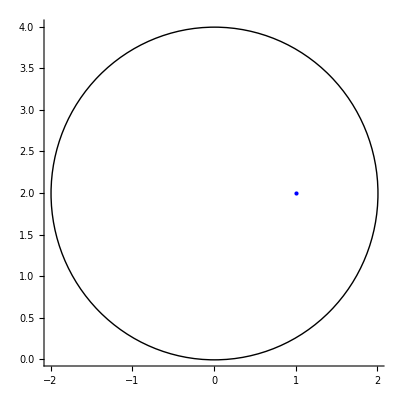

```mathematica
circle =Graphics[Circle[{0,R}, R], Axes->True];
dot=Graphics[{PointSize[Large], Blue, Point[{1, R}]}, Axes->True];
Show[circle, dot]
```

So, as this thing rotates, the y position of the dot will oscillate up and down. Note that we are taking the ground to be y=0. The x position of the dot will vary as the wheel will move right while the dot oscillates left and right as well. We can derive the following equations for the dot:


For , the first term takes into account if the dot is on the left or right side of the wheel, and the second part takes into account how far the dot has travelled in a  direction. The second term is negative since a negative rotation (rotation in ) means a movement in the  direction. In the  equation, the first term takes into account that y=0 is the ground, not the center of the wheel, and the second term takes into account where on the wheel the dot is. 

We can graph  and  over time:

```mathematica
x[t_]:=p Cos[thetaDot t] - R thetaDot t
y[t_]:=R+p Sin[thetaDot t]
Plot[{x[t], y[t]}, {t, 0, 10}, PlotLabels->"Expressions"]
```

-Graphics-

That’s no fun, nor is it easy to understand, so it’s better to plot y vs. x, or a parametric plot:

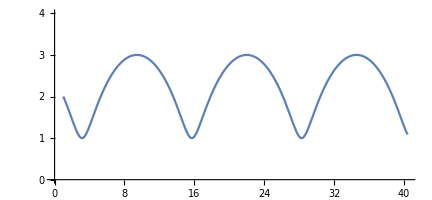

```mathematica
ParametricPlot[{x[t], y[t]}, {t, 0, 10}, PlotRange->{Automatic, {0, 4}}]
```

We can animate both of these together, so we can see how the dot moves over time (plot_xtyt.mov and paramplot_xtyt.mov):

```mathematica
plot = Plot[{x[t], y[t]}, {t, 0, 10}, PlotLabels->"Expressions"];
paramPlot=ParametricPlot[{x[t],y[t]},{t,0,10}, PlotRange->{Automatic, {0, 4}}];
Animate[
Show[plot, Graphics[{PointSize[Large],Red,Point[Dynamic[{t, x[t]}]]}], Graphics[{PointSize[Large],Red,Point[Dynamic[{t, y[t]}]]}]],{t,0,10,AppearanceElements->None}
]
Animate[Show[paramPlot,Graphics[{PointSize[Large],Red,Point[Dynamic[{x[t],y[t]}]]}]],{t,0,10,AppearanceElements->None}
]
```

This is cool, but it would be better to see the wheel rolling, so we will animate that directly (wheelroll1.mov).

```mathematica
xend = x[10];
Animate[
Show[Graphics[Circle[{d, R}, R], Axes->True, PlotRange->{{-R,xend}, {0,4}}], Graphics[{PointSize[Large],Red,Point[Dynamic[{x[t], y[t]}]]}]], 
{d, 0, xend}, {t, 0, 10}
]
```

We use two variables. The variable t is the standard time with . The variable d, however, is just the x-distance the wheel is travelling. The distance the wheel is travelling has not been parameterized in terms of t, thus we use two variables. We abuse the fact that the circle moves from 0 to the x-position of the dot at 10 seconds, . Now let’s use this animation to trace the path of the dot (wheelroll2.mov).

```mathematica
Animate[
Show[Graphics[Circle[{d, R}, R], Axes->True, PlotRange->{{-R,xend}, {0,4}}], Graphics[{PointSize[Large],Red,Point[Dynamic[{x[t], y[t]}]]}],
ParametricPlot[{x[a],y[a]},{a,0,T},PlotStyle->Thick]],
{d, 0, xend}, {t, 0, 10}, {T, 0, 10}
]
```

For parametric purposes, we introduced a t and a T. It is important to note that both of these are the same t, and we just defined them differently to not confuse Mathematica (i.e. ). Just by the nature of Mathematica and our approximation of distance for the circle rolling, we do not have a perfect animation, and it does not appear that  stays at 1 (wheelroll3.mov).

```mathematica
xcm[t_]:=-R thetaDot t
Animate[
Show[Graphics[Circle[{xcm[t], R}, R], Axes->True, PlotRange->{{-R,xend}, {0,4}}], Graphics[{PointSize[Large],Red,Point[Dynamic[{x[t], y[t]}]]}],
ParametricPlot[{x[a],y[a]},{a,0,T},PlotStyle->Thick]],
{t, 0, 10}, {T, 0, 10}
]
```

Now, instead of making an approximation of , we can just define a new function that gets the exact position of the center of the circle:

Now we use the same t parameterization for the circle as well, and this animation looks much smoother. Let’s see what we get if  and if we place our dot “outside” the circle at . Since we manually define the y-axis, we will need to do some tweaking on the hard-coded values (wheelroll_rho2.mov).

```mathematica
x2[t_]:=2 Cos[thetaDot t] - R thetaDot t
y2[t_]:=R+2 Sin[thetaDot t]
Animate[
Show[Graphics[Circle[{xcm[t], R}, R], Axes->True, PlotRange->{{-R,xend}, {0,4}}], Graphics[{PointSize[Large],Red,Point[Dynamic[{x2[t], y2[t]}]]}],
ParametricPlot[{x2[a],y2[a]},{a,0,T},PlotStyle->Thick]],
{t, 0, 10}, {T, 0, 10}
]
```

You can see that when , we get the expected “semi-circle” (a better phrasing would be semi-circle-esque).

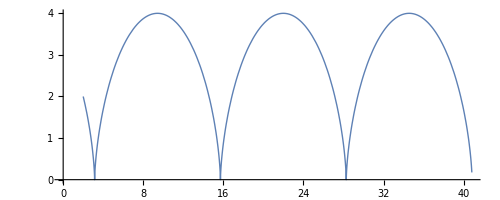

```mathematica
ParametricPlot[{x2[t],y2[t]},{t,0,10},PlotStyle->Thick]
```

```mathematica
Plot[{x2[t], y2[t]}, {t, 0, 10}, PlotLabels->"Expressions"]
```

-Graphics-

Now let’s try  (wheelroll_rho4.mov):

```mathematica
x3[t_]:=4 Cos[thetaDot t] - R thetaDot t
y3[t_]:=R+4 Sin[thetaDot t]
Animate[
Show[Graphics[Circle[{xcm[t], R}, R], Axes->True, PlotRange->{{-R,xend}, {-2,6}}], Graphics[{PointSize[Large],Red,Point[Dynamic[{x3[t], y3[t]}]]}],
ParametricPlot[{x3[a],y3[a]},{a,0,T},PlotStyle->Thick]],
{t, 0, 10}, {T, 0, 10}
]
```

Because the dot is now outside the wheel, we get this interesting non-trivial behavior where the dot is sometimes moving backwards instead of continuously forward.

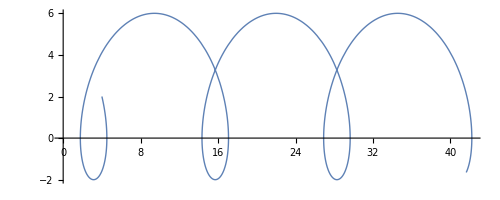

```mathematica
ParametricPlot[{x3[t],y3[t]},{t,0,10},PlotStyle->Thick]
```

```mathematica
Plot[{x3[t], y3[t]}, {t, 0, 10}, PlotLabels->"Expressions"]
```

-Graphics-

We define these as new functions  so Mathematica doesn’t mess with our other animations.

Thank you for taking interest in this project!

Copyright (c) 2023 RandomKiddo